```mathematica
1)Use HGM and NIntegrate to compute the 4-fold  integral  of the expection of an Euler characteristic number
```

```mathematica
<< RISC`HolonomicFunctions` (* load Christoph's package *)
```

HolonomicFunctions Package version 1.7.3 (21-Mar-2017)
written by Christoph Koutschan
Copyright Research Institute for Symbolic Computation (RISC),
Johannes Kepler University, Linz, Austria

--> Type  ?HolonomicFunctions  for help.

```mathematica
ann3 = << ec1_ann3.m; (* input the annihilator of the inner triple integral of Example 1*)
```

```mathematica
uts3 = UnderTheStaircase[{ann3}] (* the parametric derivatives under the stair of ann3 *)
```

{1,D_d,D_d^2,D_d^3,D_d^4,D_d^5,D_d^6,D_d^7,D_d^8,D_d^9}

```mathematica
stheta=(2 s)/(1+s^2); (* make a universal transformation for Sin[theta] *)
```

```mathematica
ctheta=(1-s^2)/(1+s^2); (* make a universal transformation for Cos[theta] *)
```

```mathematica
sphi=(2 t)/(1+t^2); (* make a universal transformation for Sin[phi] *)
```

```mathematica
cphi=(1-t^2)/(1+t^2);(* make a universal transformation for Cos[phi] *)
```

```mathematica
R=s1 (b sphi stheta+d cphi ctheta-m11)^2+s2 (-b sphi ctheta+d cphi stheta-m21)^2+s2 (b cphi ctheta+d sphi stheta-m22)^2+s1 (-b cphi stheta+d sphi ctheta)^2; (* input R in the integrand *)
```

```mathematica
f=2/(1+t^2 )2/(1+s^2) (d^2-b^2) (s1 s2)/(2 Pi)^2 Exp[-1/2 R]; (*input the integrand of Example 1*)
```

```mathematica
f1=Simplify[f/.{s1->2,s2->1,m11->1,m21->-1,m22->1}] ;(* specify the parameters as that in Example 1*)
```

```mathematica
Timing[inits = NIntegrate[Together[ApplyOreOperator[uts3,1/2 f1] /. {d -> 1/2}], {b, -Infinity, Infinity}, {s, -Infinity, Infinity}, {t, -Infinity, Infinity},MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}];] (* compute the initial value for the Pfaffian system of ann3 at d = 1/2. Since ann3 has a singularity at d = 0, it is not suitable to choose the initial point at d = 0 *)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.629452 and 0.0000229486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1055.3,Null}

```mathematica
eqnsd = ApplyOreOperator[ann3, y[d]] == 0; (* set up the differential equation for the inner triple integral *)
```

```mathematica
inits1 = Table[D[y[d], {d, i}] == inits[[i +1 ]], {i, 0, 9}] /. {d -> 1/2} (* set up the initial values for eqnsd at d = 1/2 *)
```

{y[1/2]==-0.798885,y'[1/2]==0.683103,y''[1/2]==1.32947,y^(3)[1/2]==-0.629452,y^(4)[1/2]==-4.73677,y^(5)[1/2]==-12.9357,y^(6)[1/2]==42.4342,y^(7)[1/2]==267.695,y^(8)[1/2]==-680.996,y^(9)[1/2]==-4656.36}

```mathematica
s1 = NDSolve[Join[{eqnsd},inits1], y, {d, 1/2, 30}]; (* numerical solving of the diffential equation eqnsd from 1/2 to 30 *)
```

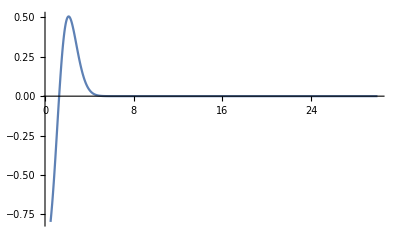

```mathematica
Plot[Evaluate[y[d]/.s1],{d,1/2,30},PlotRange->All] (* y[d] is very small when d ≥ 5*)
```

```mathematica
HGM1 = Table[NIntegrate[y[d] /. s1, {d, i, 30}][[1]], {i, 1, 6}] (* Using numerical integration to compute the integral in Example1 for x from 1 to 6. The results are as accurate as that in Prof. Kuriki's mathematica notebook*)
```

{0.745835,0.567729,0.144879,0.0146728,0.000582526,8.79942×10^-6}

```mathematica
2) Monte Carlo study for the Expectation of Euler charateristic number  of the expection of an Euler characteristic number
```

```mathematica
EulerChar[A_,x_]:=Module[{b,d,a,c},{b,d}=SingularValueList[A];(*b and d are singular value of A*)If[TrueQ[b≥x],a=Sign[b^2-d^2],a=0];
If[TrueQ[d≥x],c=Sign[d^2-b^2],c=0];
Return[a+c];]; (* compute the Euler charateristic number of a random matrix A w.r.t. x*)
```

```mathematica
Clear[s1]
```

```mathematica
sub={s1->2,s2->1,m11->1,m21->-1,m22->1}
```

{s1→2,s2→1,m11→1,m21→-1,m22→1}

```mathematica
S=DiagonalMatrix[{1/Sqrt[s1],1/Sqrt[s2]}]/.sub
```

{{1/(√2),0},{0,1}}

```mathematica
M={{m11,0},{m21,m22}}/.sub
```

{{1,0},{-1,1}}

```mathematica
n =10000000 (* the number of iterations *)
```

10000000

```mathematica
ra=Table[S.{RandomVariate[NormalDistribution[],2,WorkingPrecision->10],RandomVariate[NormalDistribution[],2,WorkingPrecision->10]}+M,{i,1,n}]; (* generate n random matrix A*)
```

```mathematica
Timing[mc = Table[ N[Sum[EulerChar[ra[[i]],x],{i,1,n}]/n], {x, 1, 6}];] (*the results of expectation of Euler characteristic number by Monte Carlo study *)
```

{2849.53,Null}

```mathematica
mc (* The results are as accurate as that in Prof. Kuriki's mathematica notebook *)
```

{0.745802,0.567623,0.144986,0.0146901,0.0005933,9.6×10^-6}